```mathematica
Remove["Global`*"]
```

```mathematica
γ=1/2;
Expγ[x_] := If[γ==0, Exp[x], (1+γ x)^(1/γ)];
Logγ[x_] := If[γ==0, Log[x], (x^γ-1)/γ];
```

```mathematica
Logγ[Expγ[y]] // PowerExpand // FullSimplify
```

y

```mathematica
Clear[CircleTimes];
CircleTimes[x_,y_] := FullSimplify[PowerExpand[Expγ[Logγ[x] + Logγ[y]]]];
```

```mathematica
X0 = 2;
x[t_, g_] := X0 ⊗ Expγ[Logγ[g] t];
```

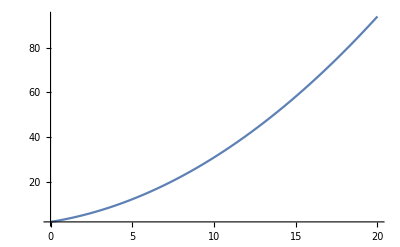

```mathematica
Plot[x[t,2], {t, 0, 20}, PlotRange->Full]
```

```mathematica
√(g^2-r^2) /. {g->21/20, r->9/20} //N
```

```mathematica
√(g^2+r^2) /.  {g->21/20, r->9/20} // N
```

1.14237

```mathematica
{g->21/20, r->9/20}
```

1.05

```mathematica
2^-T Sum[Binomial[T,n] (n a + (T-n)b)^2,{n,0,T}] // FullSimplify
```

1/4 T ((a-b)^2+(a+b)^2 T)

```mathematica
Sum[Binomial[T,n] (n a ),{n,0,T}]
```

2^(-1+T) a T

```mathematica
Sum[Binomial[T,n] ((T-n) b ),{n,0,T}]
```

2^(-1+T) b T

```mathematica
Sum[Binomial[T,n] (T b ),{n,0,T}]
```

2^T b T

```mathematica
Sum[Binomial[T,n]  (T -n)^2,{n,0,T}] // FullSimplify
```

2^(-2+T) T (1+T)

```mathematica
Collect[Expand[(n a + (T-n)b)^2], n, Simplify]
```

(a-b)^2 n^2+2 (a-b) b n T+b^2 T^2

```mathematica
(Log[√((g+r)/(g-r))]/Log[√(g^2-r^2)])^2 /. {g->21/20, r-> 9/10} // N
```

4.3536